# Optimization Methods

## CS164

Taha Bouhoun

## UNCONSTRAINED & EQUALITY CONSTRAINED OPTIMIZATION

Estimate the values of a and θ that maximize the area from your plot. Does the maximum appear to be unique over the domain of physically-realistic values? Justify your answer.

The area of the trapezoidal cross-section is expressed as:

A(a,θ)=1/2((b+(b+a×cos(θ)))×h)
A(a,θ)=1/2((2×b+a×cos(θ))×h)

we can write b and h as:

b=3-a×(sin(θ)+1)
h=a×sin(θ)
A(a,θ)=1/2((2×(3-a×(sin(θ)+1))+a×cos(θ))×a×sin(θ))

```mathematica
function[a_,θ_]:=1/2((2(3-a(Sin[θ]+1))+a Cos[θ])a Sin[θ])
```

```mathematica
Plot3D[function[a, θ],{a,0,3},{θ,0,Pi},PlotRange->Full]
```

-Graphics3D-

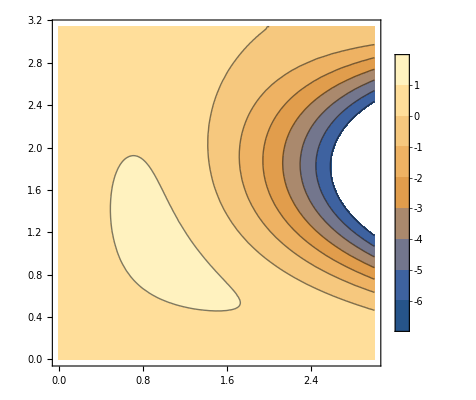

```mathematica
ContourPlot[function[a, θ],{a,0,3},{θ,0,Pi},PlotLegends->Automatic, PlotRange->Automatic]
```

To answer the question on the uniqueness of the maximum value of the function, we need to define the meaning of the physically-realistic values given the context of the problem. 

The distances a and b have to be strictly positive but also strictly less than 3 since the constraint mentioned above states that the width of the metal sheet is W = 3 m. In other words, for a and b to exist, both of them have to be strictly greater than 0 and strictly smaller than 3.

The angle θ has to be strictly greater than 0 and strictly smaller than π in order for the drainage channel to contain water. Failing to satisfy this constraint means that we can’t physically hold water within the channel.

Under the above mentioned physically-realistic constraint, we can notice that the function has a estimated maximum of a little over 1 m^2 with values of a and θ A(1, 1)

According to the contour plot, the maximum appears to be unique given the above mentioned constraint since there’s no other region that has a contour value that exceeds 1 except of the yellow shaded area around A(θ=1, a=1)

Determine whether or not the negated function −A(a, θ) is coercive, justifying your answer.

The condition for a given function to be coercive is:

In other words, the output of the function f grows to infinity when the norm constructed by its variables tends towards infinity.
Below is the contour plot of the function -A(a,θ)

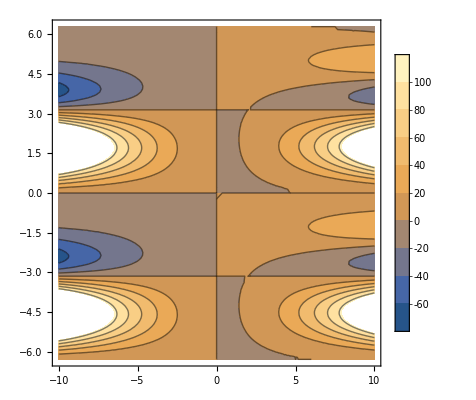

```mathematica
ContourPlot[-function[a, θ],{a,-10,10},{θ,-2*Pi,2*Pi},PlotLegends->Automatic, PlotRange->Automatic]
```

We know that the values of θ when plugged into -A(a,θ) will yield values between -1 and 1, thus, the parameter that might influence the growth of the function -A(a,θ) is the length of the segment a. However, according to the contour plot, we can see that the function doesn’t grow to infinity as we increase the value a because the function depends also on the value of the angle θ (see contour plot when θ=4 on the y-axis).
As a result, even when not considering the physically-realistic values for a and θ, the function -A(a,θ) is not growing to infinity in all directions which implies that it’s not coercive.

```mathematica
Plot3D[-function[a, θ],{a,-10,10},{θ,-2*Pi,2*Pi},PlotRange->Full]
```

-Graphics3D-

If we consider the physically-realistic constraints, then the sublevel sets of -A(a,θ) would indeed be compact. But the the sets are not closed because boundary values are not included in the domain since the distance and the angle must be strictly greater than 0 and strictly less than 3 and π respectively. As a result, the negated function is not coercive.
dom (A)=a∈]0,3[,θ∈]0,π[

Using multivariable calculus, find the exact values of a and θ that maximize the cross-sectional area of the channel. To accomplish this, consider b as a variable and use Lagrange multipliers on the area function A(a, b, θ), constraining the three variables by the width of the sheet - this will simplify calculations compared to maximizing A(a, θ) directly. Prove that the solution you found maximizes the area by applying appropriate tests, assuming the domain is restricted to physically-realistic solutions

```mathematica
Simplify[1/2((2×b+a×cos(θ))×(a×sin(θ)))]
```

1/2 a (2 b+a Cos[θ]) Sin[θ]

Objective function:
max A(a,b,θ)=1/2((2×b+a×cos(θ))×(a×sin(θ)))

Under the constraint:
a+b+a×sin(θ)-3=0

Introducing the Lagrangian Multiplier:
 L(a,b,θ,λ)=1/2((2×b+a×cos(θ))×(a×sin(θ)))−λ(a+b+asin(θ)−3)
 
 We take the gradient with respect of the variables:

```mathematica
L[a_,b_,θ_,λ_]:=1/2((2*b+a *Cos[θ])a* Sin[θ])-λ(a+b+a*Sin[θ]−3)
D[L[a,b,θ,λ],a]
D[L[a,b,θ,λ],b]
D[L[a,b,θ,λ],θ]
D[L[a,b,θ,λ],λ]
```

1/2 a Cos[θ] Sin[θ]+1/2 (2 b+a Cos[θ]) Sin[θ]-λ (1+Sin[θ])

-λ+a Sin[θ]

-a λ Cos[θ]+1/2 a Cos[θ] (2 b+a Cos[θ])-1/2 a^2 Sin[θ]^2

3-a-b-a Sin[θ]

We then solve for the derivatives to be equal to zero:

```mathematica
Solve[D[L[a,b,θ,λ],a]==0,{a,b,θ,λ},Reals]
Solve[D[L[a,b,θ,λ],b]==0,{a,b,θ,λ},Reals]
Solve[D[L[a,b,θ,λ],θ]==0,{a,b,θ,λ},Reals]
Solve[D[L[a,b,θ,λ],λ]==0,{a,b,θ,λ},Reals]
```

We can exclude the first solution since θ can’t be equal to π . Furthermore, The second solution appears to consider b as a negative metric which contradict with the physically-realistic assumptions.
The last options seems to satisfy all constraint listed in part I, below is the numerical values of A(a,b,θ),a,b, and θ

```mathematica
N[L[4Sqrt[3]-6,3-Sqrt[3],Pi/3,6-3Sqrt[3]]]
N[4Sqrt[3]-6]
N[3-Sqrt[3]]
N[Pi/3]
```

1.20577

0.928203

1.26795

1.0472

Considering once again the function A(a, θ), implement gradient ascent with a line search (exact or backtracking) in Python and from the initial state (1.5, 0), verify that you reach the same optimal solution. Produce a table of steps showing how the algorithm converges, and plot the convergence over the contour plot of A(·, ·)

Using the NMaximizer function in Mathematica

```mathematica
NMaximize[{function[a,θ],0<a<3,0<θ<Pi},{a,θ}]
NMaximize[{function[a,θ],0<a<3,0<θ<Pi,3-a (Sin[θ]+1)>0},{a,θ}]
```

{1.20577,{a→0.928203,θ→1.0472}}

{1.20577,{a→0.928203,θ→1.0472}}

# Gradient ascent in Python

x1 = np.array([])
x2 = np.array([])
x = np.array([1.5, 0])
tol = np.inf
k = 0
store = []
step = 0.01


while tol >= 1e-5:
    x_new = x + step * grad_f(x)
    x1 = np.append(x1, x_new[0])
    x2 = np.append(x2, x_new[1])
    tol = np.linalg.norm(x_new - x, 2)
    x = x_new
    store.append(np.append(x, f(x)))
    k+=1
    
print("\nFunction Value: ", f(x), "\nAt X = ", x, " after", k, "iterations")

Function Value:  1.2057704755756375 
At X =  [0.92920329 1.04570113]  after 1167 iterations


			a		θ	A(a, θ)
0		1.500000	0.033750	0.111301
1		1.500472	0.065944	0.212509
2		1.501327	0.096594	0.304217
3		1.502487	0.125722	0.387050
4		1.503877	0.153360	0.461646
5		1.505434	0.179547	0.528643
6		1.507099	0.204330	0.588668
7		1.508824	0.227757	0.642329
8		1.510564	0.249882	0.690208
9		1.512284	0.270761	0.732853
10		1.513952	0.290451	0.770780
------------------------------------------
1156		0.929260	1.045616	1.205770
1157		0.929254	1.045625	1.205770
1158		0.929248	1.045634	1.205770
1159		0.929243	1.045642	1.205770
1160		0.929237	1.045651	1.205770
1161		0.929231	1.045659	1.205770
1162		0.929226	1.045668	1.205770
1163		0.929220	1.045676	1.205770
1164		0.929214	1.045685	1.205770
1165		0.929209	1.045693	1.205770
1166		0.929203	1.045701	1.205770

# Gradient ascent with a line search (backtracking) in Python

def backtrack_line_search(f, grad_f, x, alpha=.5, beta=.5, eps=1e-6):
    direction = grad_f(x)/lp.norm(grad_f(x))
    d = np.dot(grad_f(x).T, direction)
    step_size = 1
    while f(x + step_size * direction) < f(x) + step_size * alpha * d:
        step_size *= beta
        if step_size * lp.norm(direction) < eps: break
    return step_size

  
x1 = np.array([])
x2 = np.array([])
x = np.array([1.5, 0])
tol = np.inf
store = []
k = 0


while tol >= 1e-5:
    step = backtrack_line_search(f, grad_f, x)
    x_new = x + step * grad_f(x) / lp.norm(grad_f(x))
    x1 = np.append(x1, x_new[0])
    x2 = np.append(x2, x_new[1])
    tol = np.linalg.norm(x_new - x, 2)
    x = x_new
    store.append(np.append(x, f(x)))
    k+=1
    
print("\nFunction Value: ", f(x), "\nAt X = ", x, " after", k, "iterations")

Function Value:  1.205771365797318 
At X =  [0.92821686 1.04717959]  after 25 iterations

		a		θ	A(a, θ)
0	1.500000	0.500000	1.034875
1	1.489436	0.624553	1.083232
2	1.246216	0.682380	1.140715
3	1.223727	0.805341	1.162833
4	1.161409	0.800571	1.174824
5	0.976284	0.968585	1.203345
6	0.972523	0.999608	1.204489
7	0.957194	1.002632	1.204988
8	0.945919	1.031777	1.205562
9	0.938147	1.030982	1.205671
10	0.935954	1.038481	1.205730
11	0.932148	1.039361	1.205748
12	0.932390	1.041299	1.205757
13	0.929676	1.044108	1.205768
14	0.929869	1.045065	1.205769
15	0.929016	1.045541	1.205770
16	0.929092	1.046023	1.205771
17	0.928687	1.046296	1.205771
18	0.928687	1.046540	1.205771
19	0.928306	1.046846	1.205771
20	0.928370	1.046950	1.205771
21	0.928229	1.047150	1.205771
22	0.928229	1.047165	1.205771
23	0.928215	1.047172	1.205771
24	0.928217	1.047180	1.205771